```mathematica
(*kies latent=3, infectious=10*)
```

# A model for the spread of corona virus: R0

```mathematica
date=DateString[{"Day","Month","YearShort"}]
```

130720

```mathematica
AspRat=0.75;
ImSize=400;
```

```mathematica
filepath="/Users/mirjam/Projects/Corona/LancetPHpaper/Hypercuberesults/";
```

```mathematica
scenariocontactred={1.0,0.95,0.9,0.85,0.8,0.75,0.7,0.65,0.6,0.55,0.5,0.45,0.4,0.35,0.3,0.25,0.2,0.15,0.1,0.05};
(*probtransm[pt_,declinetransm_,infectious_]:=Table[Min[1.0,pt*tau*Exp[-tau*declinetransm]], {tau,1,infectious}];*)
probtransm[pt_,infectious_,αinfection_,βinfection_]:=Block[{q},
q=0.5*Table[CDF[WeibullDistribution[αinfection,βinfection]][i+0.5]-CDF[WeibullDistribution[αinfection,βinfection]][i-.5],{i,1,infectious}]+
0.35*Table[CDF[WeibullDistribution[αinfection,βinfection]][i+0.5]-CDF[WeibullDistribution[αinfection,βinfection]][i-.5],{i,2,infectious+1}]+
0.15*Table[CDF[WeibullDistribution[αinfection,βinfection]][i+0.5]-CDF[WeibullDistribution[αinfection,βinfection]][i-.5],{i,3,infectious+2}]
;
q=q/Total[q]*pt*0.4586584744929515/0.1211
](*Note latency period of 1 day*)

rzero[pt_,contactdist1_,contactdist2_,transratio_,infectious_,αinfection_,βinfection_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt,infectious,αinfection,βinfection][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt,infectious,αinfection,βinfection][[i]])
```

```mathematica
rzero1[pt_,contactdist1_,declinetransm_,infectious_]:=∑_(i=1)^infectious Mean[contactdist1[[i]]]*probtransm[pt,infectious,αinfection,βinfection][[i]]
```

```mathematica
rzero2[pt_, contactdist2_,transratio_,infectious_,αinfection_,βinfection_]:=∑_(i=1)^infectious Mean[contactdist2[[i]]]*probtransm[transratio*pt,infectious,αinfection,βinfection][[i]]
ratiohousehold[pt_,contactdist1_,contactdist2_,transratio_,infectious_,αinfection_,βinfection_]:=rzero1[pt,contactdist1,infectious,αinfection,βinfection]/(rzero1[pt,contactdist1,infectious,αinfection,βinfection]+rzero2[pt, contactdist2,transratio,infectious,αinfection,βinfection]);
rzeroday[pt_,contactdist1_,contactdist2_,transratio_,infectious_,αinfection_,βinfection_]:=Table[Mean[contactdist1[[i]]]*probtransm[pt,infectious,αinfection,βinfection][[i]]+Mean[contactdist2[[i]]]*probtransm[pt,infectious,αinfection,βinfection][[i]]*transratio, {i,1,infectious}]
probdiagapp[fa_,probsymp_,infectious_]:=Table[Table[If[i<ds ,0.0,fa*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
probtrace[vd_,cv_,fa_,pd_,timewindow_,transmissionweights_,infectious_]:=fa*Table[Flatten[{Table[∑_(j=i)^Min[i-1+Length[pd[[ds,i]]],i+timewindow] pd[[ds,i,j-i+1]]*cv*transmissionweights[[j+vd-1]],{i,1,infectious-1}],0}],{ds,1,infectious}];
reffiso[pt_,ds_,infectious_,contactdist1_,contactdist2_,transratio_,probdiag_,infectious_,αinfection_,βinfection_]:=∑_(i=1)^infectious ((Mean[contactdist1[[i]]]*probtransm[pt,infectious,αinfection,βinfection][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt,infectious,αinfection,βinfection][[i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
reffvacc1[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_,infectious_,contactdist1_,contactdist2_,transratio_,probdiag_,pd_,timewindow_,transmissionweights_,αinfection_,βinfection_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt,infectious,αinfection,βinfection][[i]]*(1-probtrace[vd1,cv1,fa,pd,timewindow,transmissionweights,infectious][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc2[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_,infectious_,contactdist1_,contactdist2_,transratio_,probdiag_,pd_,timewindow_,transmissionweights_,αinfection_,βinfection_]:=∑_(i=1)^infectious ( Mean[contactdist2[[i]]]*probtransm[transratio*pt,infectious,αinfection,βinfection][[i]]*(1-probtrace[vd2,cv2,fa,pd,timewindow,transmissionweights,infectious][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_,infectious_,contactdist1_,contactdist2_,transratio_,probdiag_,pd_,timewindow_,transmissionweights_,αinfection_,βinfection_]:=reffvacc1[pt,vd1,vd2,cv1,cv2,ds,fa,infectious,contactdist1,contactdist2,transratio,probdiag,pd,timewindow,transmissionweights,αinfection,βinfection]+reffvacc2[pt,vd1,vd2,cv1,cv2,ds,fa,infectious,contactdist1,contactdist2,transratio,probdiag,pd,timewindow,transmissionweights,αinfection,βinfection]
```

0.8

{2.96592,7.17059}

{0.0583185,0.0922551,0.12083,0.135036,0.12998,0.107731,0.0764756,0.046117,0.0233897,0.00986727}

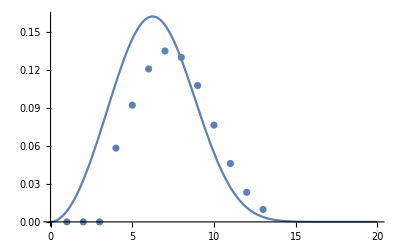

```mathematica
(*translate probdevelopingsymptoms into probsymp *)
(*Stel 80% krijgt symptomen *)
(*tijd tot symptomen gegeven symptomen is een Weibull verdeling met parameters (α1,β1)*)
latent=3;
m=6.4;
sd=2.35;
psymptoms=0.8
{αsymptoms,βsymptoms}={α,β}/.FindRoot[{m==β Gamma[1+1/α],sd^2==β^2 (-Gamma[1+1/α]^2+Gamma[1+2/α])},{{α,1},{β,6.2}}]

shape=Table[CDF[WeibullDistribution[αsymptoms,βsymptoms]][i+0.5]-CDF[WeibullDistribution[αsymptoms,βsymptoms]][i-.5],{i,3,12}];
probdevelopingsymptoms=psymptoms*shape/Total[shape]
Show[Plot[PDF[WeibullDistribution[αsymptoms,βsymptoms]][x],{x,0,20}],ListPlot[Join[{0,0,0},probdevelopingsymptoms]]]
qq[1]=probdevelopingsymptoms[[1]];
Do[qq[i]=probdevelopingsymptoms[[i]]/Product[(1-qq[j]),{j,1,i-1}],{i,2,10}]
probsymp=Table[qq[i],{i,1,10}];
```

```mathematica
(*best-fit Weibull distribution model was estimated at 4.6 days (95% CI:3.5,5.9) with a mean and SD of 4.8 days (95% CrI:3.8,6.1) and 2.3 days (95% CrI:1.6,3.5)
Nishiura 2020, Serial interval of novel coronavirus (COVID-19) infections*)
m=4.8;
sd=2.3;
{αinfection,βinfection}={α,β}/.FindRoot[{m==β Gamma[1+1/α],sd^2==β^2 (-Gamma[1+1/α]^2+Gamma[1+2/α])},{{α,1},{β,6.2}}]
```

{2.20339,5.41988}

```mathematica
FindRoot[CDF[NormalDistribution[4.8,(m-llm)/1.96]][y]==0.2,{y,4.8}]
```

FindRoot::nlnum: The function value {-0.2+1/2 Erfc[-(9.91294×10^-8)/(4.8+Times[«2»])]} is not a list of numbers with dimensions {1} at {y} = {4.8}.

{y→4.8}

```mathematica
probtransm[1.0,10,2.2033912982247017,5.419875286500868]
```

{0.348446,0.531887,0.634637,0.6393,0.560803,0.434692,0.299959,0.184989,0.10216,0.0505619}

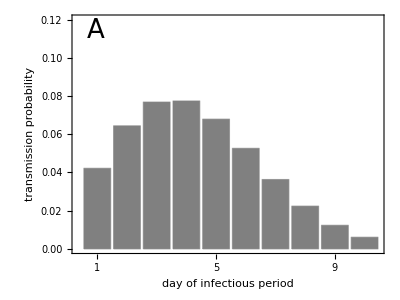

```mathematica
Show[BarChart[probtransm[0.1211,10,2.2033912982247017,5.419875286500868],AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{All,{0.0,0.12}},ChartStyle->GrayLevel[0.5],Frame->True, FrameTicks->{{True,None},{Table[i,{i,1,20}],None}}, FrameStyle->Directive[Black,17],FrameLabel->{"day of infectious period", "transmission probability"}],Graphics[Text[StyleForm["A",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,0.12*0.95}]]]
```

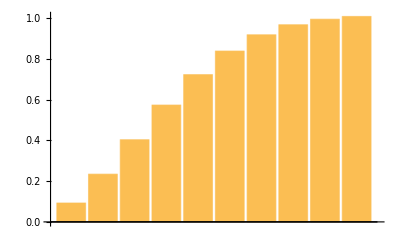

```mathematica
BarChart[Table[Sum[probtransm[0.1211,10,2.2033912982247017,5.419875286500868][[i]],{i,1,j}],{j,1,10}]/Sum[probtransm[0.12,10,2.2033912982247017,5.419875286500868][[i]],{i,1,10}]]
```

```mathematica
shape
```

{0.0693622,0.109725,0.143711,0.160607,0.154594,0.128132,0.0909577,0.0548501,0.027819,0.0117358}

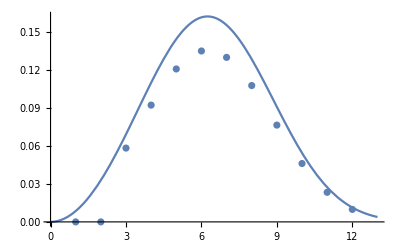

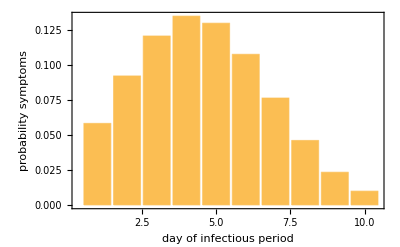

```mathematica
(*Time to developing symptoms by time since becoming infectious*)
probdevelopingsymptoms=psymptoms*shape/Total[shape];
Show[ListPlot[Join[{0,0},probdevelopingsymptoms]],Plot[PDF[WeibullDistribution[αsymptoms,βsymptoms]][x],{x,0,13}],PlotRange->{{0,13},All}]
plotprobsymptoms=BarChart[probdevelopingsymptoms, Frame->True,ChartLabels->Table[i,{i,1,infectious}],FrameLabel->{"day of infectious period", "probability symptoms"},FrameTicks->{{True,None},{True,None}},FrameStyle->Directive["Label",16]]
```

```mathematica
(*Mean=4.8 days 95% CI (3.8,6.1)
sd=2.3 days (95% CrI:1.6,3.5)*)

generatedata[m_,ll_,ul_,n_]:=Block[{lijst,rn,i,r},
lijst={};
rn=RandomReal[{0,1},n];
Do[
If[rn[[i]]<0.5, r=Max[0,y/.FindRoot[CDF[NormalDistribution[m,(m-ll)/1.96]][y]==rn[[i]],{y,m}]],
r=y/.FindRoot[CDF[NormalDistribution[m,(-m+ul)/1.96]][y]==rn[[i]],{y,m}];
];
lijst={lijst,{r}}
,{i,1,n}];
lijst=Flatten[lijst]
]
```

```mathematica
minfection=generatedata[4.8,3.8,6.1,1000];
sdinfection=generatedata[2.3,1.6,3.5,1000];
msymptoms=generatedata[6.4,5.6,7.7,1000];
sdsymptoms=generatedata[2.3,1.7,3.7,1000];
```

```mathematica
converttoweibull[listm_,listsd_]:=Block[{αi,βi,listalpha,listbeta},
listalpha={};listbeta={};
Do[
{αi,βi}={α,β}/.FindRoot[{listm[[i]]==β Gamma[1+1/α],listsd[[i]]
^2==β^2 (-Gamma[1+1/α]^2+Gamma[1+2/α])},{{α,1},{β,6.2}}];
listalpha={listalpha,{αi}};
listbeta={listbeta,{βi}};
,{i,1,Length[listm]}];
listalpha=Flatten[listalpha];
listbeta=Flatten[listbeta];
{listalpha,listbeta}
]
```

```mathematica
{listalphainfection,listbetainfection}=converttoweibull[minfection,sdinfection];
{listalphasymptoms,listbetasymptoms}=converttoweibull[msymptoms,sdsymptoms];
Export[StringJoin[filepath,"/minfection.txt"],minfection,"Table"];
Export[StringJoin[filepath,"/sdinfection.txt"],sdinfection,"Table"];
Export[StringJoin[filepath,"/msymptoms.txt"],msymptoms,"Table"];
Export[StringJoin[filepath,"/sdsymptoms.txt"],sdsymptoms,"Table"];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
reffv[meanhouseholdcontacts_,negbinn_,negbinp_
,infectious_,casefatality_,transratio_,
transmissibility_,fractest_,timewindow_,vaccdelay2_,vaccdelay3_,coverage2_,coverage3_,diagdelay_,
αinfection_,βinfection_,αsymptoms_,βsymptoms_,psymptoms_
]:=
Block[{scenarioasymptomatic,factorasymptomatic,contactreduction1,contactreduction2,probinf,probsymp,probdevelopingsymptoms,fraccas,saturation1,saturation2,
mu1,mu2,contactdist1,contactdist2,contact,numcontacts,meancontacts,stdcontacts,rzeroperc,rzerocum,probdiag,probbeingdiagnosed,cumprobbeingdiagnosed,pd,sums,rzerodayprob,cumrzerodayprob,transmissionweights,startinf,shape,qq,q,latent},
latent=3;
contactreduction1=scenariocontactred[[9]];
contactreduction2=scenariocontactred[[15]];
probinf=Flatten[Append[Table[0.0,{i,1,latent-3}],{0.5,0.7,1.0}]];
(*shape=Table[CDF[WeibullDistribution[αsymptoms,βsymptoms]][i+0.5]-CDF[WeibullDistribution[αsymptoms,βsymptoms]][i-.5],{i,latent,infectious+latent-1}];*)
shape=0.5*Table[CDF[WeibullDistribution[αsymptoms,βsymptoms]][i+0.5]-CDF[WeibullDistribution[αsymptoms,βsymptoms]][i-.5],{i,1,infectious}]+
0.35*Table[CDF[WeibullDistribution[αsymptoms,βsymptoms]][i+0.5]-CDF[WeibullDistribution[αsymptoms,βsymptoms]][i-.5],{i,2,infectious+1}]+
0.15*Table[CDF[WeibullDistribution[αsymptoms,βsymptoms]][i+0.5]-CDF[WeibullDistribution[αsymptoms,βsymptoms]][i-.5],{i,3,infectious+2}]
;


probdevelopingsymptoms=psymptoms*shape/Total[shape];
qq[1]=probdevelopingsymptoms[[1]];
qq[2]=probdevelopingsymptoms[[2]];
Do[qq[i]=probdevelopingsymptoms[[i]]/Product[(1-qq[j]),{j,2,i-1}],{i,3,infectious}];
probsymp=Table[qq[i],{i,1,infectious}];
saturation1=Drop[Prepend[Table[Product[1-probtransm[transmissibility,infectious,αinfection,βinfection][[j]],{j,1,i}],{i,1,infectious}],1.0],-1];
saturation2=Drop[Prepend[Table[Product[1-probtransm[transmissibility*transratio,infectious,αinfection,βinfection][[j]],{j,1,i}],{i,1,infectious}],1.0],-1];
mu1=meanhouseholdcontacts*saturation1*contactreduction1;
mu2=negbinn*saturation2*contactreduction2;
contactdist1=Array[f,infectious];
contactdist2=Array[f,infectious];
For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}];
contact=Array[f,latent+infectious];
For [i=1,i≤infectious,i++,contact[[i]]=Mean[contactdist1[[i]]]+Mean[contactdist2[[i]]]];
numcontacts=Table[RandomVariate[contactdist1[[i]],1000]+RandomVariate[contactdist2[[i]],1000],{i,1,infectious}];
meancontacts=Table[Mean[numcontacts[[i]]],{i,1,infectious}]//N;
stdcontacts=Table[StandardDeviation[numcontacts[[i]]],{i,1,infectious}]//N;
rzeroperc=rzeroday[transmissibility,contactdist1,contactdist2,transratio,infectious,αinfection,βinfection]/rzero[transmissibility,contactdist1,contactdist2,transratio,infectious,αinfection,βinfection]*100;
rzerocum=Table[∑_(i=1)^j rzeroperc[[i]], {j,1,infectious}];
probdiag=Table[Table[If[i<ds ,0.0,fractest*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
probbeingdiagnosed=Table[Table[Product[(1-probdiag[[ds,j-1]]),{j,2,i}]*probdiag[[ds,i]],{i,1,infectious}],{ds,1,infectious}];
cumprobbeingdiagnosed=Table[Table[Sum[probbeingdiagnosed[[j,k]],{k,1,i}],{i,1,infectious}],{j,1,infectious}];
pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
sums=Table[∑_(k=1)^(infectious-j) pd[[1,j,k]],{j,1,infectious-1}];
rzerodayprob=rzeroday[transmissibility,contactdist1,contactdist2,transratio,infectious,αinfection,βinfection]/rzero[transmissibility,contactdist1,contactdist2,transratio,infectious,αinfection,βinfection];
cumrzerodayprob=Table[Sum[rzerodayprob[[j]],{j,1,i}],{i,1,infectious}];
startinf=Table[Product[(1-probinf[[k-1]]),{k,2,j}]*probinf[[j]],{j,1,latent}];
transmissionweights=PadRight[1-Total[Table[startinf[[k]]*PadLeft[Drop[cumrzerodayprob,-k],infectious],{k,1,latent}]],infectious+timewindow];
reffvacc1[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractest,infectious,contactdist1,contactdist2,transratio,probdiag,pd,timewindow,transmissionweights,αinfection,βinfection]
]
```

```mathematica
reffv[4.,1.6,0.15,
10,0.02,0.25,
0.1211,1.,7,1.,1.,1.,
1.,1,
2.2033912982247017,5.419875286500868,2.9659217893126293,7.170585371529246,0.8]
```

0.51329

```mathematica
i=1;
listalphainfection[[i]]
listbetainfection[[i]]
listalphasymptoms[[i]]
listbetasymptoms[[i]]
Length[listalphainfection]
```

2.51037

6.25993

2.75295

6.80783

1000

```mathematica
n=1000;
meanhouseholdcontacts=4;
negbinn=1.6;
negbinp=0.15;
infectious=10;
casefatality=0.02;
transratio=0.25;
transmissibility=0.1211;
fractest=0.8;
timewindow=7;
coverage2=0.8;
coverage3=0.8;
psymptoms=0.8;



ParallelDo[
Do[
Print["k=",k];
l=Table[reffv[meanhouseholdcontacts,negbinn,negbinp,
infectious,casefatality,transratio,
transmissibility,fractest,timewindow,k,k,1.,
1.,dd,
listalphainfection[[i]],listbetainfection[[i]],listalphasymptoms[[i]],listbetasymptoms[[i]],psymptoms],{i,1,n}];
Export[filepath<>"/dd"<>ToString[dd]<>"k"<>ToString[k]<>"1000.txt",l,"Table"];
,{k,1,4}];

l=Table[reffv[meanhouseholdcontacts,negbinn,negbinp,
infectious,casefatality,transratio,
transmissibility,fractest,timewindow,1,1,0.,
0.,dd,
listalphainfection[[i]],listbetainfection[[i]],listalphasymptoms[[i]],listbetasymptoms[[i]],psymptoms],{i,1,n}];
Export[filepath<>"/isodd"<>ToString[dd]<>"1000.txt",l,"Table"];

,{dd,1,8}];
```

k=1

k=1

k=1

«3 more identical outputs»

k=2

k=2

k=2

«3 more identical outputs»

k=3

k=3

k=3

«3 more identical outputs»

k=4

k=4

k=4

«3 more identical outputs»

k=1

k=1

k=2

k=2

k=3

k=3

k=4

k=4

```mathematica
dd
```

dd

```mathematica
factor=.91/.68/1.0226872033857919*1.014;
Do[
Do[

ll[dd,k]=Sort[Flatten[Import[filepath<>"/dd"<>ToString[dd]<>"k"<>ToString[k]<>"1000.txt","Table"]]];
mm[dd,k]=factor*Mean[ll[dd,k]];
lr[dd,k]=factor*(ll[dd,k][[Floor[0.025*Length[ll[dd,k]]]]]+
ll[dd,k][[1+Floor[0.025*Length[ll[dd,k]]]]])/2;
ur[dd,k]=factor*(ll[dd,k][[Ceiling[0.975*Length[ll[dd,k]]]]]+
ll[dd,k][[1+Ceiling[0.975*Length[ll[dd,k]]]]])/2;
,{k,1,4}];
iso[dd]=Sort[Flatten[Import[filepath<>"/isodd"<>ToString[dd]<>"1000.txt","Table"]]];
miso[dd]=factor*Mean[iso[dd]];
lriso[dd]=factor*(iso[dd][[Floor[0.025*Length[iso[dd]]]]]+
iso[dd][[1+Floor[0.025*Length[iso[dd]]]]])/2;
uriso[dd]=factor*(iso[dd][[Ceiling[0.975*Length[iso[dd]]]]]+
iso[dd][[1+Ceiling[0.975*Length[iso[dd]]]]])/2;


,{dd,1,8}];
```

```mathematica
mm[3,2]
lr[3,2]
ur[3,2]
```

1.0265

0.923004

1.12242

```mathematica
miso[8]
```

1.19925

```mathematica
grid1=1.2
```

1.2

```mathematica
factor2=grid1/miso[8]
```

1.00063

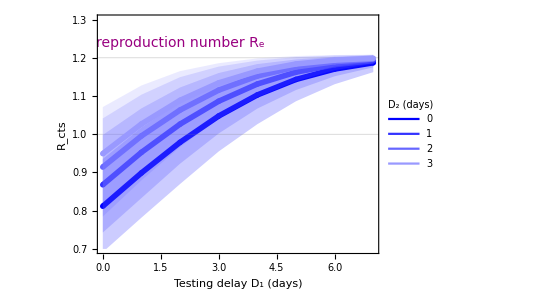

```mathematica
colors= {Red,Green,Blue,Orange};
colors= Table[RGBColor[(k-1) 0.2,0.2( k-1),1],{k,{1,2,3,4}}];
legend3=LineLegend[ Table[RGBColor[(k-1) 0.2,0.2( k-1),1],{k,{1,2,3,4}}],Table[j,{j,{0,1,2,3}}],LegendLabel->"D_2 (days)",LabelStyle->Directive[Black,14], LegendMargins->5];
legend3=LineLegend[colors,Table[j,{j,{0,1,2,3}}],LegendLabel->"D_2 (days)",LabelStyle->Directive[Black,14], LegendMargins->5];
labelgraph="Fraction symptomatic tested ";
yrange={0.7,1.3};
figure2=Show[Table[ListPlot[{Table[{dd-1,mm[dd,k]},{dd,1,8}],Table[{dd-1,ur[dd,k]},{dd,1,8}],Table[{dd-1,lr[dd,k]},{dd,1,8}]},PlotRange->{All,yrange},Joined->True,PlotMarkers->{"OpenMarkers",None,None},PlotStyle->{{colors[[k]],Thickness[0.01]},None,None},Filling->{3->{2}},FillingStyle->{Opacity[0.2,colors[[k]]]},GridLines->{None,{{grid1,{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractest*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],{k,{1,2,3,4}}],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,grid1+0.04}]],Graphics[Inset[legend3,{6.0,0.84}]]]
```

```mathematica
figureisolation= ListPlot[{Table[{dd-1,miso[dd]},{dd,1,8}],Table[{dd-1,uriso[dd]},{dd,1,8}],Table[{dd-1,lriso[dd]},{dd,1,8}]},PlotRange->{All,yrange},Joined->True,PlotMarkers->{"OpenMarkers",None,None},PlotStyle->{{RGBColor[0,0.4,0],Thickness[0.01]},None,None},Filling->{3->{2}},FillingStyle->{Opacity[0.2,RGBColor[0,0.4,0]]},LabelStyle->{RGBColor[0,0.4,0],14},PlotLabels->Placed["isolation",{Scaled[0.14],Top}]];
```

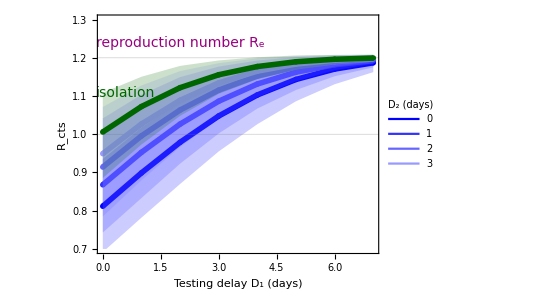

```mathematica
figurecoverage=Show[figure2,figureisolation,FrameTicks->{{Automatic,None},{Automatic,None}}]
```

```mathematica
Export[StringJoin[filepath,"/figurecoveragehypercube.pdf"],figurecoverage,"PDF"]
```

/Users/mirjam/Projects/Corona/LancetPHpaper/Hypercuberesults//figurecoveragehypercube.pdf

```mathematica
covvalues={2,4,6,8}
```

{2,4,6,8}

```mathematica
n=1000;
meanhouseholdcontacts=4;
negbinn=1.6;
negbinp=0.15;
infectious=10;
casefatality=0.02;
transratio=0.25;
transmissibility=0.1211;
fractest=0.8;
timewindow=7;
coverage2=0.8;
coverage3=0.8;
psymptoms=0.8;
k=3;
ParallelDo[
Do[
l=Table[reffv[meanhouseholdcontacts,negbinn,negbinp,
infectious,casefatality,transratio,
transmissibility,fractest,timewindow,1,1,fractionapp*(1-(k-1)*0.1),
fractionapp*(1-(k-1)*0.1),dd,
listalphainfection[[i]],listbetainfection[[i]],listalphasymptoms[[i]],listbetasymptoms[[i]],psymptoms],{i,1,n}];
Export[filepath<>"/covdd"<>ToString[dd]<>"k"<>ToString[k]<>"1000.txt",l,"Table"];
,
{k,covvalues}],
{dd,1,8}]
```

```mathematica
factor=.91/.68/1.0226872033857919*1.014;
Do[
Do[

ll[dd,k]=Sort[Flatten[Import[filepath<>"/covdd"<>ToString[dd]<>"k"<>ToString[k]<>"1000.txt","Table"]]];
mcov[dd,k]=factor*Mean[ll[dd,k]];
lrcov[dd,k]=factor*(ll[dd,k][[Floor[0.025*Length[ll[dd,k]]]]]+
ll[dd,k][[1+Floor[0.025*Length[ll[dd,k]]]]])/2;
urcov[dd,k]=factor*(ll[dd,k][[Ceiling[0.975*Length[ll[dd,k]]]]]+
ll[dd,k][[1+Ceiling[0.975*Length[ll[dd,k]]]]])/2;
,{k,covvalues}];
,{dd,1,8}];
```

```mathematica
urcov[3,3]
```

urcov[3,3]

{2,4,6,8}

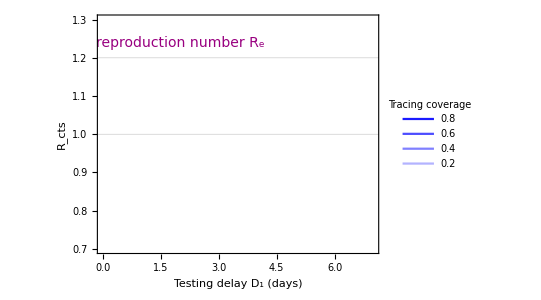

```mathematica
covvalues={2,4,6,8}
col[2]=RGBColor[(1-1) 0.2,0.2( 1-1),1];
col[4]=RGBColor[(2-1) 0.2,0.2( 2-1),1];
col[6]=RGBColor[(3-1) 0.2,0.2( 3-1),1];
col[8]=RGBColor[(4-1) 0.2,0.2( 4-1),1];
legend4=LineLegend[ Table[RGBColor[(k-1) 0.1,0.1( k-1),1],{k,covvalues}],Table[NumberForm[1*(1-(j)*0.1),{2,1}],{j,covvalues}],LegendLabel->"Tracing coverage",LabelStyle->Directive[Black,14], LegendMargins->5];
colors= {Red,Green,Blue,Orange};
colors= Table[RGBColor[(k-1) 0.2,0.2( k-1),1],{k,{1,2,3,4}}];
legend3=LineLegend[ Table[RGBColor[(k-1) 0.2,0.2( k-1),1],{k,{1,2,3,4}}],Table[j,{j,{0,1,2,3}}],LegendLabel->"D_2 (days)",LabelStyle->Directive[Black,14], LegendMargins->5];
legend3=LineLegend[colors,Table[j,{j,{0,1,2,3}}],LegendLabel->"D_2 (days)",LabelStyle->Directive[Black,14], LegendMargins->5];
labelgraph="Fraction symptomatic tested ";
yrange={0.7,1.3};
figure1=Show[Table[ListPlot[{Table[{dd-1,mcov[dd,k]},{dd,1,8}],Table[{dd-1,urcov[dd,k]},{dd,1,8}],Table[{dd-1,lrcov[dd,k]},{dd,1,8}]},PlotRange->{All,yrange},Joined->True,PlotMarkers->{"OpenMarkers",None,None},PlotStyle->{{col[k],Thickness[0.01]},None,None},Filling->{3->{2}},GridLines->{None,{{grid1,{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, 

FillingStyle->{Opacity[0.2,col[k]]},FrameLabel->{{ Text[Subscript[R,cts]],None},{"Testing delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractest*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],{k,covvalues}],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,grid1+0.04}]],Graphics[Inset[legend4,{5.5,0.84}]]]
```

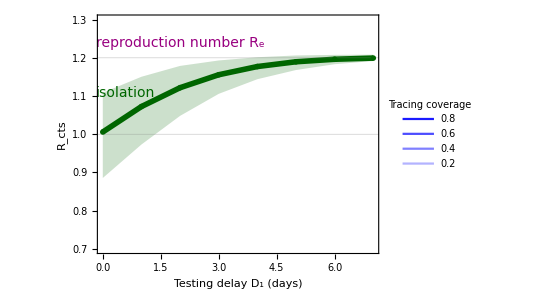

```mathematica
figuretracingdelay=Show[figure1,figureisolation,FrameTicks->{Automatic, Automatic, None, None}]
```

```mathematica
Export[StringJoin[filepath,"/figuretracingdelayhypercube.pdf"],figuretracingdelay,"PDF"]
```

/Users/mirjam/Projects/Corona/LancetPHpaper/Hypercuberesults//figuretracingdelayhypercube.pdf

```mathematica
n=1000;
meanhouseholdcontacts=4;
negbinn=1.6;
negbinp=0.15;
infectious=10;
casefatality=0.02;
transratio=0.25;
transmissibility=0.1211;
fractest=0.8;
timewindow=7;
coverage2=0.8;
coverage3=0.8;
psymptoms=0.8;
ParallelDo[
Print[dd];
l=Table[reffv[meanhouseholdcontacts,negbinn,negbinp,
infectious,casefatality,transratio,
transmissibility,0.8,timewindow,1,1,1,
1,dd,
listalphainfection[[i]],listbetainfection[[i]],listalphasymptoms[[i]],listbetasymptoms[[i]],psymptoms],{i,1,n}];
Export[filepath<>"/fig40dd"<>ToString[dd]<>"1000.txt",l,"Table"];
l=Table[reffv[meanhouseholdcontacts,negbinn,negbinp,
infectious,casefatality,transratio,
transmissibility,0.8,timewindow,1,1,0.8,
0.8,dd,
listalphainfection[[i]],listbetainfection[[i]],listalphasymptoms[[i]],listbetasymptoms[[i]],psymptoms],{i,1,n}];
Export[filepath<>"/fig41dd"<>ToString[dd]<>"1000.txt",l,"Table"];
l=Table[reffv[meanhouseholdcontacts,negbinn,negbinp,
infectious,casefatality,transratio,
transmissibility,0.8,timewindow,1,1,0.6,
0.6,dd,
listalphainfection[[i]],listbetainfection[[i]],listalphasymptoms[[i]],listbetasymptoms[[i]],psymptoms],{i,1,n}];
Export[filepath<>"/fig42dd"<>ToString[dd]<>"1000.txt",l,"Table"];
l=Table[reffv[meanhouseholdcontacts,negbinn,negbinp,
infectious,casefatality,transratio,
transmissibility,0.8,timewindow,4,4,0.8,
0.5,dd,
listalphainfection[[i]],listbetainfection[[i]],listalphasymptoms[[i]],listbetasymptoms[[i]],psymptoms],{i,1,n}];
Export[filepath<>"/fig43dd"<>ToString[dd]<>"1000.txt",l,"Table"];

,
{dd,1,8}]
```

1

3

5

6

7

8

4

2

```mathematica
factor=.91/.68/1.0226872033857919*1.014;
Do[
ll[dd]=Sort[Flatten[Import[filepath<>"/fig40dd"<>ToString[dd]<>"1000.txt","Table"]]];
mfig40[dd]=factor*Mean[ll[dd]];
lrfig40[dd]=factor*(ll[dd][[Floor[0.025*Length[ll[dd]]]]]+
ll[dd][[1+Floor[0.025*Length[ll[dd]]]]])/2;
urfig40[dd]=factor*(ll[dd][[Ceiling[0.975*Length[ll[dd]]]]]+
ll[dd][[1+Ceiling[0.975*Length[ll[dd]]]]])/2;
ll[dd]=Sort[Flatten[Import[filepath<>"/fig41dd"<>ToString[dd]<>"1000.txt","Table"]]];
mfig41[dd]=factor*Mean[ll[dd]];
lrfig41[dd]=factor*(ll[dd][[Floor[0.025*Length[ll[dd]]]]]+
ll[dd][[1+Floor[0.025*Length[ll[dd]]]]])/2;
urfig41[dd]=factor*(ll[dd][[Ceiling[0.975*Length[ll[dd]]]]]+
ll[dd][[1+Ceiling[0.975*Length[ll[dd]]]]])/2;
ll[dd]=Sort[Flatten[Import[filepath<>"/fig42dd"<>ToString[dd]<>"1000.txt","Table"]]];
mfig42[dd]=factor*Mean[ll[dd]];
lrfig42[dd]=factor*(ll[dd][[Floor[0.025*Length[ll[dd]]]]]+
ll[dd][[1+Floor[0.025*Length[ll[dd]]]]])/2;
urfig42[dd]=factor*(ll[dd][[Ceiling[0.975*Length[ll[dd]]]]]+
ll[dd][[1+Ceiling[0.975*Length[ll[dd]]]]])/2;
ll[dd]=Sort[Flatten[Import[filepath<>"/fig43dd"<>ToString[dd]<>"1000.txt","Table"]]];
mfig43[dd]=factor*Mean[ll[dd]];
lrfig43[dd]=factor*(ll[dd][[Floor[0.025*Length[ll[dd]]]]]+
ll[dd][[1+Floor[0.025*Length[ll[dd]]]]])/2;
urfig43[dd]=factor*(ll[dd][[Ceiling[0.975*Length[ll[dd]]]]]+
ll[dd][[1+Ceiling[0.975*Length[ll[dd]]]]])/2;



,{dd,1,8}];
```

```mathematica
urfig40[1] 
mfig40[1]
lrfig40[1]
```

0.93505

0.811733

0.691612

```mathematica
urfig41[1] 
mfig41[1]
lrfig41[1]
```

0.970016

0.850565

0.733256

```mathematica
uriso[1]
miso[1]
lriso[1]
```

1.10858

1.00589

0.885559

```mathematica
miso[8]
```

1.20099

```mathematica
colors= {RGBColor[0,0.2,1],RGBColor[0,0.4,1],RGBColor[0.0,0.6,1],RGBColor[1,0.5,0.0]}
```

{RGBColor[0, 0.2, 1],RGBColor[0, 0.4, 1],RGBColor[0., 0.6, 1],RGBColor[1, 0.5, 0.]}

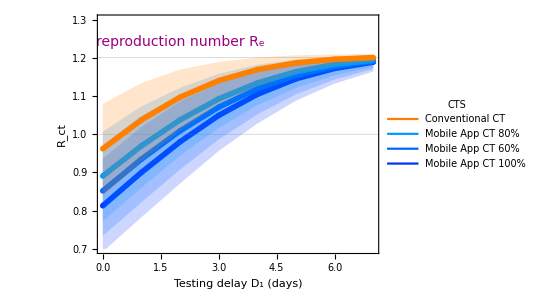

```mathematica
colors= {RGBColor[0,0.2,1],RGBColor[0,0.4,1],RGBColor[0.0,0.6,1],RGBColor[1,0.5,0.0]};

legend1=LineLegend[{RGBColor[1, 0.49, 0],RGBColor[0,0.6,1],RGBColor[0,0.4,1],RGBColor[0.0,0.2,1]},{ "Conventional CT","Mobile App CT 80%", "Mobile App CT 60%","Mobile App CT 100%"},LegendLabel->"CTS",LabelStyle->Directive[GrayLevel[0],14],LegendMargins->5]
labelgraph="Fraction symptomatic tested ";
yrange={0.7,1.3};
figure4=Show[Table[ListPlot[{Table[{dd-1,ToExpression["mfig4"<>ToString[k-1]][dd]},{dd,1,8}],Table[{dd-1,ToExpression["urfig4"<>ToString[k-1]][dd]},{dd,1,8}],Table[{dd-1,ToExpression["lrfig4"<>ToString[k-1]][dd]},{dd,1,8}]},PlotRange->{All,yrange},Joined->True,PlotMarkers->{"OpenMarkers",None,None},PlotStyle->{{colors[[k]],Thickness[0.01]},None,None},Filling->{3->{2}},GridLines->{None,{{grid1,{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}},Frame->True, 

FillingStyle->{Opacity[0.2,colors[[k]]]},FrameLabel->{{ Text[Subscript[R,ct]],None},{"Testing delay D_1 (days)" ,StringJoin[labelgraph,ToString[Ceiling[fractionapp*100]],"%"]}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None},AspectRatio->AspRat,ImageSize->ImSize],{k,1,4}],Graphics[Text[Style["reproduction number R_e",Directive[RGBColor[3* 0.2,0.0,0.5],14]],{2
,grid1+0.04}]],Graphics[Inset[legend1,{5.0,0.84}]]]
```

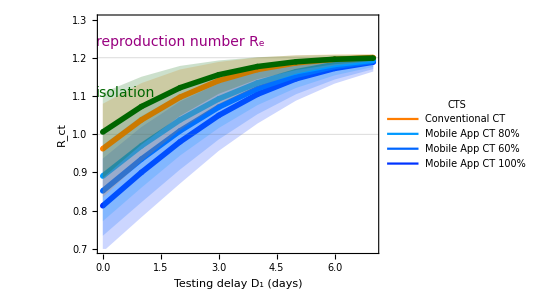

```mathematica
figure3apaper=Show[figure4,figureisolation,PlotRange->{{0,7},{0.7,1.3}},FrameTicks->{Automatic, Automatic, None, None},GridLines->{None,{{grid1,{RGBColor[3* 0.2,0.0,0.5],Thickness[0.007]}},{1,{Red,Thickness[0.007]}}}}]
```

```mathematica
Export[StringJoin[filepath,"/figure3apaperhypercube.pdf"],figure3apaper,"PDF"]
```

/Users/mirjam/Projects/Corona/LancetPHpaper/Hypercuberesults//figure3apaperhypercube.pdf